```mathematica
"Leah Dougherty
ChE 272 Final Project
March 4, 2009
Part II"
```

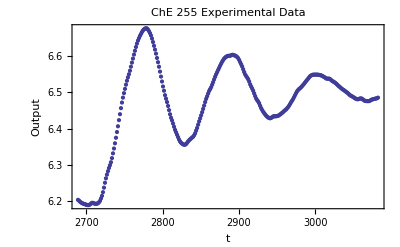

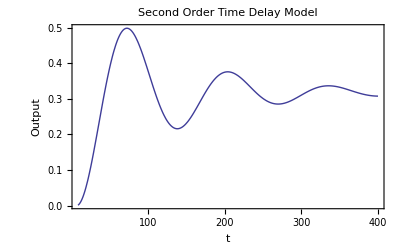

```mathematica
θ=6;
kc=10;
tau1=90;
tau2=50;
taui=0.1;

(*Use of the Pade Approximation for Time Delay*)
Pade[s]=(θ^2/12*s^2-θ/2*s+1)/(θ^2/12*s^2+θ/2*s+1);

gp[s]=Pade[s]/((tau1*s+1)*(tau2*s+1));

(*The 3 Different Kinds of Controllers*)

gcPI[s]=(kc*(taui*s+1))/(taui*s+1);


sProcess=(gp[s]*gcPI[s])/(1+(gp[s]*gcPI[s]))*0.35/s;

tProcess=InverseLaplaceTransform[sProcess,s,t];

(*Imported Experimental Data from LabView*)
ListPlot[Import["ChE 272 Data.csv"], FrameLabel->{"t","Output"}, PlotRange->All, PlotLabel->Style["ChE 255 Experimental Data",16], LabelStyle->Directive[Bold,12], Frame->True]

Plot[tProcess,{t,0,400}, FrameLabel->{"t","Output"},PlotStyle->{Thick}, PlotRange->All, PlotLabel->Style[ "Second Order Time Delay Model",16], LabelStyle->Directive[Bold,12], Frame->True]
```